## Using PRIMAT to plot abundances as function of η=n_b/n_γ

### Loading PRIMAT

Setting the notebook directory (in batch mode this is not evaluated because it seems to be the default one)

```mathematica
SetDirectory[NotebookDirectory[]];
```

Then we go the parent directory, or base directory of PRIMAT.

```mathematica
SetDirectory[ParentDirectory[Directory[]]]
```

/Users/pitrou/Dropbox/iap/notebooks/BBN

We load PRIMAT. It takes some time because it starts reading the file with nuclear reactions and deduces which are the nuclides needed, 
and it starts to build formally the network of equations

```mathematica
Timing[<<PRIMAT-Main.m]
```

{16.8608,Null}

## Dependence on baryons abundance

#### Set - up

We change the baryon numbers and re-run the numerical integrations of differential equations so as to build plots of abundances as a function of baryons.

We parallelize and for each point in η we perform a MOnte-Carlo on reaction rates to estimate uncertainty

```mathematica
$ParallelBool=True;

$RandomNuclearRates=True;
$Randomτneutron=True;
$Randomh2Ωb=False;
```

Table of 10^10η values for which we need the abundances to be computed with our code.

```mathematica
Tableη=Table[10^leta,{leta,-10,-9,0.05(*0.05*)}];
```

This function returns the final abundances for a given η parameter. It evaluates the uncertainty by doing a Monte-Carlo on nuclear rates and on τ_neutron.

```mathematica
ComputePrincipalAbundanceBaryons[η_]:=Module[{ResultMean,Resultσ,Meanh2Ωb0Old},
Meanh2Ωb0Old=Meanh2Ωb0;
Meanh2Ωb0=Ωbh2Overη η;

RunPRIMATMonteCarlo[LengthMC];

YP=4ElementColumn["a"];
YDH=10^5 ElementColumn["d"]/ElementColumn["p"];
YHe3H=10^5(ElementColumn["t"]+ElementColumn["He3"])/ElementColumn["p"];
YLi7H=10^10(ElementColumn["Li7"]+ElementColumn["Be7"])/ElementColumn["p"];

Meanh2Ωb0=Meanh2Ωb0Old;

{YP,YDH,YHe3H,YLi7H}

]
```

And we apply it to the table of η parameters. The result is a table of abundances for all η parameters.

```mathematica
LengthMC=1000;
MachineNumerics=""(*$MachineName*);
```

We run the MonteCarlo for all η. This can take ages (hours at least)

```mathematica
Timing[TableYsLowMiddleUp=ComputePrincipalAbundanceBaryons/@Tableη;];
Export["MonteCarlo/YsEta"<>MachineNumerics<>".mx",TableYsLowMiddleUp,"MX"];
```

Running a Monte-Carlo with 2 points.

$Aborted

#### Organizing results

Once the run is finished we can load the result. We need to give the name of the machine on which it was run (or rename the file YsEtaxxx).

```mathematica
MachineOfRuns="";
```

```mathematica
TableYsLowMiddleUp=Import["MonteCarlo/YsEta"<>MachineOfRuns<>".mx"];
```

```mathematica
TableYsLowMiddleUp//Dimensions
```

{21,4,1000}

We attribute the results to low middle and high values.

```mathematica
MyPair[a_,b_]:={a,b};
ValueLow[i_]:=Interpolation@Thread[MyPair[Tableη*10^10,Flatten[Quantile[#,{0.15865}]&/@TableYsLowMiddleUp[[All,i]]]]]
ValueMiddle[i_]:=Interpolation@Thread[MyPair[Tableη*10^10,Flatten[Quantile[#,{0.50}]&/@TableYsLowMiddleUp[[All,i]]]]]
ValueHigh[i_]:=Interpolation@Thread[MyPair[Tableη*10^10,Flatten[Quantile[#,{1-0.15865}]&/@TableYsLowMiddleUp[[All,i]]]]]
```

For instance ValueLow[1] gives the low values of Helium4, ValueLow[2]  for D/H, ValueLow[3] for He3/H and ValueLow[4] for Li7/H

We define some ticks for the plot so as to show both η and Ω_b h^2 nicely

```mathematica
Tickseta={1,2,3,4,5,6,7,8,9,10};
Ticksetah2Ωb={1,2,3,4,6,8};
Tikcsh2Ωb=Transpose[{Ticksetah2Ωb, ToString/@N@Round[10^-10 Ticksetah2Ωb*Ωbh2Overη,10^-4]}];
MyTicks2={{Automatic,Automatic},{Tickseta,Tikcsh2Ωb}};
```

```mathematica
MyTicks3={{Automatic,Automatic},{Tickseta,{{0.004/Ωbh2Overη*10^10,"0.004"},{0.005/Ωbh2Overη*10^10,""},{0.006/Ωbh2Overη*10^10,""},{0.007/Ωbh2Overη*10^10,""},{0.008/Ωbh2Overη*10^10,""},{0.009/Ωbh2Overη*10^10,""},{0.01/Ωbh2Overη*10^10,"0.01"},{0.011/Ωbh2Overη*10^10,""},{0.012/Ωbh2Overη*10^10,""},{0.013/Ωbh2Overη*10^10,""},{0.014/Ωbh2Overη*10^10,""},{0.015/Ωbh2Overη*10^10,""},{0.016/Ωbh2Overη*10^10,""},{0.017/Ωbh2Overη*10^10,""},{0.018/Ωbh2Overη*10^10,""},{0.019/Ωbh2Overη*10^10,""},{0.02/Ωbh2Overη*10^10,"0.02"},{0.021/Ωbh2Overη*10^10,""},{0.022/Ωbh2Overη*10^10,""},{0.023/Ωbh2Overη*10^10,""},{0.024/Ωbh2Overη*10^10,""},{0.025/Ωbh2Overη*10^10,""},{0.026/Ωbh2Overη*10^10,""},{0.027/Ωbh2Overη*10^10,""},{0.028/Ωbh2Overη*10^10,""},{0.029/Ωbh2Overη*10^10,""},{0.03/Ωbh2Overη*10^10,"0.03"},{0.04/Ωbh2Overη*10^10,"0.04"}}}};
```

```mathematica
MyTicks4={{Automatic,Automatic},{Tickseta,None}};
MyTicksHe4={{{{0.222,""},{0.224,""},{0.226,""},{0.228,""},0.23,{0.232,""},{0.234,""},{0.236,""},{0.238,""},{0.232,""},0.24,{0.242,""},{0.244,""},{0.246,""},{0.248,""},0.25,{0.252,""},{0.254,""},{0.256,""},{0.258,""},0.26},Automatic},{Tickseta,None}};
```

Planck bounds

```mathematica
Meanh2Ωb0=Meanh2Ωb0Planck
ηPlanckmin=(Meanh2Ωb0-σh2Ωb0)/Ωbh2Overη
ηPlanckmax=(Meanh2Ωb0+σh2Ωb0)/Ωbh2Overη
```

0.02225

6.04753×10^-10

6.13514×10^-10

#### Plots

He4 plot

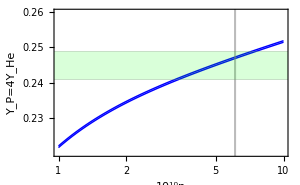

```mathematica
HeliumEta=Show[LogLinearPlot[{ValueLow[1][η10],ValueHigh[1][η10]},{η10,1,10},Frame->True,Filling->{1->{2}},ImagePadding->{{55,7},{0,6}},ImageSize->300,FrameLabel->{"10^10η","Y_P=4Y_He"},LabelStyle->{FontSize->12},PlotStyle->{{Blue,Thin},{Blue,Thin}},FrameTicks->MyTicksHe4,GridLines->{{{10^10 ηPlanckmin,{Darker@Gray}},{10^10 ηPlanckmax,{Darker@Gray}}},{{(0.2449-0.0040) ,{Green}},{(0.2449+0.0040) ,{Green}}}},PlotRange->{{1,10},{0.22,0.26}},PlotRangePadding->None,FrameStyle->Thickness[0.004]],
Graphics[{Opacity[0.5],Gray,Rectangle[{Log[10^10 ηPlanckmin],Log[.1]},{Log[10^10 ηPlanckmax],Log[100]}],
Opacity[0.15],Green,Rectangle[{Log[0.8],0.2449-0.0040},{Log[14],0.2449+0.0040}],Opacity[1],Black,Rotate[Text[Style["",FontSize->16,Black],{Log[10^10 ηPlanckmin],0.23}],90 Degree]}]]

Export["Plots/PlotHeliumEta.pdf",Style[HeliumEta,Magnification->1],"PDF"];
```

He3 and Deuterium

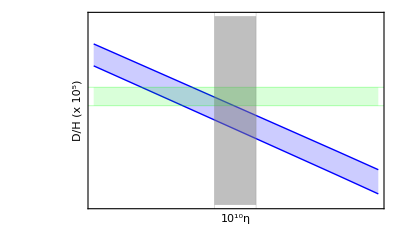

```mathematica
MyInset=Show[LogLogPlot[{ValueLow[2][η10],ValueHigh[2][η10]},{η10,5.8,6.4},Frame->True,FrameTicks->{{{2.3,2.5,2.7},Automatic},{{5.8,6.0,6.2,6.4},None}},Filling->{1->{2}},PlotRange->{{5.8,6.4},{2.2,2.8}},PlotStyle->{{Blue,Thin},{Blue,Thin},{Blue,Thin},{Blue,Thin}},FrameLabel->{"10^10η","D/H  (x 10^5)"},LabelStyle->{FontSize->8},GridLines->{{{10^10 ηPlanckmin,{Darker@Gray}},{10^10 ηPlanckmax,{Darker@Gray}}},{{(2.527-0.030) ,Green},{(2.527+0.030) ,Green},{(0.9) ,{Green}},{(1.3) ,{Green}}}}],
Graphics[{Opacity[0.5],Gray,Rectangle[{Log[10^10 ηPlanckmin],Log@2.2},{Log[10^10 ηPlanckmax],Log[2.8]}],
Opacity[0.15],Green,Rectangle[{Log@5.8,Log[2.527-0.030]},{Log@6.4,Log[2.527+0.030]}]}]]
```

He3 and deuterium plot

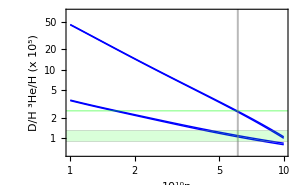

```mathematica
He3Eta=Show[LogLogPlot[{ValueLow[2][η10],ValueHigh[2][η10],ValueLow[3][η10],ValueHigh[3][η10]},{η10,1,10},Frame->True,ImageSize->300,ImagePadding->{{55,7},{0,0}},Filling->{1->{2},3->{4}},FrameLabel->{"10^10η","D/H      ^3He/H  (x 10^5)"},LabelStyle->{FontSize->12},PlotStyle->{{Blue,Thin},{Blue,Thin},{Blue,Thin},{Blue,Thin}},
Epilog->Inset[MyInset,{Log@3.5,3.},Automatic,.9],PlotRange->{{1,10},{0.6,70}},PlotRangePadding->None,
FrameTicks->MyTicks4,FrameStyle->Thickness[0.004],GridLines->{{{10^10 ηPlanckmin,{Darker@Gray}},{10^10 ηPlanckmax,{Darker@Gray}}},{{(2.527-0.030) ,Green},{(2.527+0.030) ,Green},{(0.9) ,{Green}},{(1.3) ,{Green}}}}],
Graphics[{Opacity[0.5],Gray,Rectangle[{Log[10^10 ηPlanckmin],Log[.1]},{Log[10^10 ηPlanckmax],Log[100]}],
Opacity[0.15],LightGreen,Rectangle[{Log[0.8],Log[2.527-0.030]},{Log[14],Log[2.527-0.030]}],
Opacity[0.15],Green,Rectangle[{Log[0.8],Log[0.9]},{Log[14],Log[1.3]}],
Black,Opacity[0.8],Rotate[Text[Style["",FontSize->16,Black],{Log[10^10 ηPlanckmin],Log[.6 10^-4*10^5]}],90 Degree]}]]

Export["Plots/PlotHelium3DeuteriumEta.pdf",Style[He3Eta,Magnification->1],"PDF"];
```

Li7. It seems that we have a problem here...

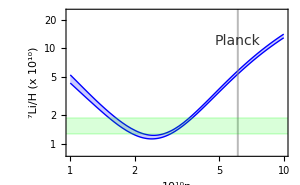

```mathematica
Li7Eta=Show[LogLogPlot[{ValueLow[4][η10],ValueHigh[4][η10]},{η10,1,10},Frame->True,Filling->{1->{2}},ImagePadding->{{55,7},{40,0}},ImageSize->300,FrameLabel->{"10^10η","^7Li/H   (x 10^10)"},LabelStyle->{FontSize->12},PlotStyle->{{Thin,Blue},{Thin,Blue}},FrameTicks->MyTicks4,GridLines->{{{10^10 ηPlanckmin,{Darker@Gray}},{10^10 ηPlanckmax,{Darker@Gray}}},{{(1.58-0.3) ,Green},{(1.58+0.3) ,Green}}},PlotRange->{{1,10},{0.8,24}},PlotRangePadding->None,FrameStyle->Thickness[0.004]],
Graphics[{Opacity[0.5],Gray,Rectangle[{Log[10^10 ηPlanckmin],Log[.1]},{Log[10^10 ηPlanckmax],Log[30]}],
Opacity[0.15],Green,Rectangle[{Log[0.8],Log[1.58-0.3]},{Log[14],Log[1.58+0.3]}],
Black,Opacity[0.8],Rotate[Text[Style["Planck",FontSize->14,Black],{Log[10^10 ηPlanckmin],Log[1.2 10^-9*10^10]}],90 Degree]}]]

Export["Plots/PlotLithium7Eta.pdf",Style[Li7Eta,Magnification->1],"PDF"];
```

Stakcing all plots

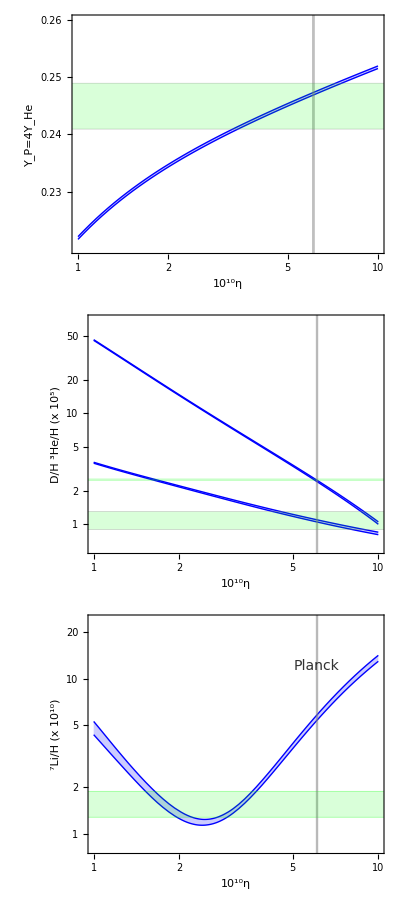

```mathematica
Column[{HeliumEta,He3Eta,Li7Eta},Spacings->0]
Export["Plots/GridAbundances.pdf",Style[%,Magnification->1],"PDF"];
```